```mathematica
(* some helper code for working with training sets, hyperplanes, and generated data*)
hyperplaneQ[{x_?VectorQ,bias_?NumericQ}] := True;
hyperplaneQ[y_]:=False;
bias[plane_?hyperplaneQ]:=plane⟦2⟧;
weights[plane_?hyperplaneQ]:=plane⟦1⟧;
```

```mathematica
labelQ[x_] := x === 1 || x === -1;
trainingExampleQ [{x___List,y_?labelQ}] := True
trainingExampleQ[x_] := False
trainingSetQ[{x___?trainingExampleQ}] := True
trainingSetQ[y_] := False

getPoints[trainingSet_?trainingSetQ]:=Map[First,trainingSet];
getLabels[trainingSet_?trainingSetQ]:=Flatten[Map[Rest,trainingSet]];
```

```mathematica
(* gives a list of points corresponding to a specific label *)
filterByLabel[trainingSet_, label_?labelQ]:=
getPoints[Select[trainingSet,#⟦2⟧==label&]];

(* gives the training points separated by label *)
getPointsByLabel[trainingSet_] := Map[filterByLabel[trainingSet,#]&,DeleteDuplicates[getLabels[trainingSet]]];

GenerateData2D[decisionFun_, count_,{xMin_, xMax_},{yMin_, yMax_}] := 
With[{points = Table[{Random[Real, {xMin, xMax}], Random[Real, {yMin, yMax}]},{count}]},
Map[{#,If[decisionFun[#] < 0,-1,1]}&,points]]

PlotData[data_?trainingSetQ]:=ListPlot[getPointsByLabel[data],PlotStyle->{PointSize[0.02]},AspectRatio->Automatic]
```

```mathematica
generatingFunction[{x_,y_}] := x+y-1;
data=GenerateData2D[generatingFunction, 25, {0,1},{0,1}];
```

```mathematica
DecisionRegionPlot[data_,plane_?hyperplaneQ,{xMin_,xMax_},{yMin_, yMax_}]:=
Show[RegionPlot[weights[plane].{x,y} + bias[plane]>= 0,
{x,xMin,xMax},{y,yMin,yMax}],PlotData[data]];
```

```mathematica
(* Perceptron algorithm *)
ϵ = 0.01;
initialHyperplane = {{ϵ,ϵ},ϵ};
```

```mathematica
isMisclassified[plane_?hyperplaneQ,{point_,label_}]:=
label*(weights[plane].point+bias[plane]) ≤ 0;

misclassifiedDelta[plane_?hyperplaneQ,{point_,label_}]:={label*point,label};
```

```mathematica
(* the inner loop of the pseudocode *)
doUpdate[data_?trainingSetQ, plane_?hyperplaneQ]:= 
With[{updateIfMisclassified = #1+If[isMisclassified[#1,#2],misclassifiedDelta[#1,#2],0]&},
Fold[updateIfMisclassified,plane,data]
];
```

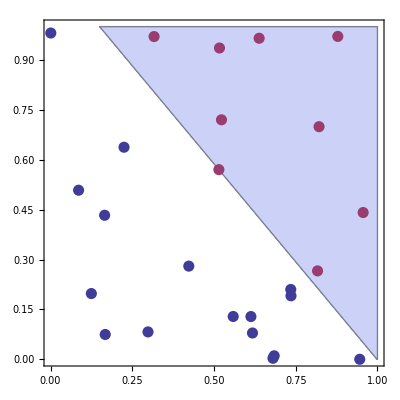

{{4.99795,4.24015},-4.99}

```mathematica
(* the outer loop of the pseudocode *)
learn[data_?trainingSetQ]:=NestWhile[doUpdate[data,#]&,initialHyperplane, #1≠#2&,2];
DecisionRegionPlot[data,learn[data],{0,1},{0,1}]
finalPlane=learn[data]
```

```mathematica
decisionFun=#.finalPlane⟦1⟧+finalPlane⟦2⟧&;
```

Generalization has an accuracy of 92.2%

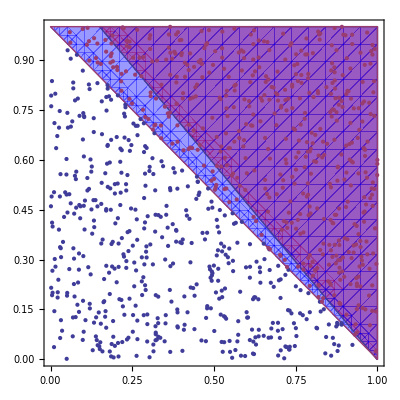

```mathematica
(* functions for tesing generalization propeties *)
TestGeneralization[decisionFunction_, newData_]:=
Module[{testPoint, lst},
testPoint[x_, label_]:=If[Sign[decisionFunction[x]]==label,1,0];
lst = MapThread[testPoint,{getPoints[newData], getLabels[newData]}];
Print["Generalization has an accuracy of " <> ToString[100.*Apply[Plus,lst]/Length[lst]] <> "%"];
];

DisplayBoundary[decisionFunction_, generatingFunction_,trainingSet_, {xMin_, xMax_}, {yMin_, yMax_}] := 
Show[RegionPlot[{decisionFunction[{x,y}] > 0, generatingFunction[{x,y}] > 0}, {x,xMin,xMax},{y,yMin,yMax},PlotStyle->{Directive[Red,Opacity[0.4]],Directive[Blue,Opacity[0.4]]}],ListPlot[getPointsByLabel[trainingSet]]];

newData = GenerateData2D[generatingFunction, 1000, {0,1},{0,1}];
TestGeneralization[decisionFun, newData];
DisplayBoundary[decisionFun, generatingFunction, newData,{0,1},{0,1}]
```

```mathematica
deleteDoubles[{x_,x_,rest___}]:=deleteDoubles[{x,rest}];
deleteDoubles[{x_,rest___}]:=Join[{x},deleteDoubles[{rest}]];
deleteDoubles[{}]:={};
```

```mathematica
deleteDoubles[{{1,2},{1,2},3,4,5,5,6,6,7}]
```

{{1,2},3,4,5,6,7}

```mathematica
(* special code for animations, saving all the intermediate hyperplanes *)
doUpdate2[data_?trainingSetQ, plane_?hyperplaneQ]:= 
With[{updateIfMisclassified=#1+If[isMisclassified[#1,#2],misclassifiedDelta[#1,#2],0]&},
FoldList[updateIfMisclassified,plane,data]
];
```

```mathematica
intermediateHyperplanes={initialHyperplane};
Module[{last=initialHyperplane,updateResult},
While[Length[intermediateHyperplanes]==1 || last≠intermediateHyperplanes⟦-1⟧,
updateResult = doUpdate2[data,intermediateHyperplanes⟦-1⟧];
last=updateResult⟦1⟧;
intermediateHyperplanes=Join[intermediateHyperplanes⟦;;-2⟧,deleteDoubles[updateResult]];]]
Length[intermediateHyperplanes]
```

80

```mathematica
frames=Map[DecisionRegionPlot[data,#,{0,1},{0,1}]&,Join[intermediateHyperplanes,Table[intermediateHyperplanes⟦-1⟧,{10}]]];
Export["perceptron-iterations.gif",frames,"DisplayDurations"->0.25];
```